```mathematica
resource=ResourceObject["MNIST"];
trainingData=ResourceData[resource,"TrainingData"];
testData=ResourceData[resource,"TestData"];
```

```mathematica
Length[trainingData]
```

60000

```mathematica
Length[testData]
```

10000

```mathematica
trainingData[[22000]]  (*X -> Y*)
```

-Graphics-→3

```mathematica
x=trainingData[[22000]]
```

-Graphics-→3

0.0745098

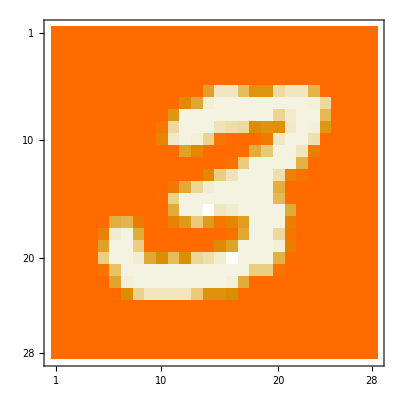

```mathematica
xim = ImageData[First[x]];
xim[[10,20]]
MatrixPlot[xim]
```

```mathematica
xim //MatrixForm
```

(1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.541176 | 0.0784314 | 0.0784314 | 0.388235 | 0.615686 | 0.615686 | 0.14902 | 0.0784314 | 0.0784314 | 0.447059 | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.705882 | 0.505882 | 0.0313725 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.0156863 | 0.160784 | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.603922 | 0.00784314 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.192157 | 0.0470588 | 0.00392157 | 0.00392157 | 0.415686 | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.886275 | 0.156863 | 0.00392157 | 0.00392157 | 0.00392157 | 0.101961 | 0.137255 | 0.152941 | 0.678431 | 0.623529 | 0.643137 | 0.0705882 | 0.00392157 | 0.0117647 | 0.603922 | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.729412 | 0.054902 | 0.00392157 | 0.0196078 | 0.203922 | 0.890196 | 1. | 1. | 1. | 0.811765 | 0.0745098 | 0.00392157 | 0.00392157 | 0.113725 | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.52549 | 0.686275 | 1. | 1. | 1. | 0.984314 | 0.486275 | 0.290196 | 0.00392157 | 0.00392157 | 0.0862745 | 0.815686 | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.94902 | 0.254902 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.458824 | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.709804 | 0.25098 | 0.0941176 | 0.00392157 | 0.00392157 | 0.00392157 | 0.117647 | 0.780392 | 0.909804 | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.858824 | 0.494118 | 0.188235 | 0.0352941 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.47451 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.968627 | 0.223529 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.411765 | 0.956863 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.486275 | 0.00392157 | 0.00392157 | 0. | 0.0823529 | 0.0392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.494118 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 0.47451 | 0.431373 | 0.847059 | 1. | 1. | 0.776471 | 0.568627 | 0.278431 | 0.568627 | 0.882353 | 0.717647 | 0.552941 | 0.00392157 | 0.00392157 | 0.00392157 | 0.784314 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 0.772549 | 0.0392157 | 0.00392157 | 0.486275 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.945098 | 0.498039 | 0.00392157 | 0.00392157 | 0.160784 | 0.890196 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 0.537255 | 0.00392157 | 0.00392157 | 0.247059 | 1. | 1. | 1. | 1. | 1. | 1. | 0.698039 | 0.52549 | 0.00392157 | 0.00392157 | 0.00392157 | 0.0196078 | 0.796078 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 0.243137 | 0.00392157 | 0.00392157 | 0.0313725 | 0.498039 | 0.670588 | 0.396078 | 0.658824 | 0.188235 | 0.133333 | 0.0352941 | 0. | 0.00392157 | 0.00392157 | 0.00392157 | 0.462745 | 0.968627 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 0.901961 | 0.356863 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00784314 | 0.247059 | 0.247059 | 0.898039 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 0.521569 | 0.027451 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.00392157 | 0.0196078 | 0.482353 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 0.682353 | 0.211765 | 0.0823529 | 0.0823529 | 0.0823529 | 0.0823529 | 0.27451 | 0.623529 | 0.623529 | 0.662745 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

```mathematica
ximv  = Flatten[Join[xim]];
Length[ximv]
```

784

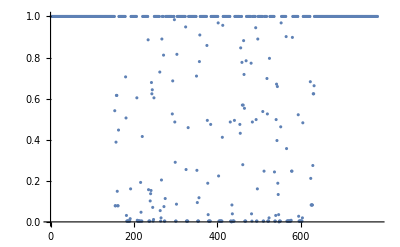

```mathematica
ListPlot[ximv]
```

```mathematica
28*28
```

784

```mathematica
lenet=NetChain[
{ConvolutionLayer[20,5],
Ramp,PoolingLayer[2,2],
ConvolutionLayer[50,5],
Ramp,
PoolingLayer[2,2],
FlattenLayer[],
500,
Ramp,
10,
SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",Range[0,9]}],"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]]
```

NetChain[<>]

```mathematica
?NetTrain
```

```mathematica
lenet=NetTrain[lenet,trainingData,ValidationSet->testData,MaxTrainingRounds->3];
```

```mathematica
lenet
```

NetChain[<>]

```mathematica
imgs=Keys@RandomSample[testData,30];
Thread[imgs->lenet[imgs]]
```

{-Graphics-→1,-Graphics-→2,-Graphics-→5,-Graphics-→1,-Graphics-→5,-Graphics-→2,-Graphics-→9,-Graphics-→7,-Graphics-→8,-Graphics-→2,-Graphics-→7,-Graphics-→1,-Graphics-→4,-Graphics-→1,-Graphics-→9,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→8,-Graphics-→5,-Graphics-→3,-Graphics-→1,-Graphics-→9,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→1,-Graphics-→5,-Graphics-→2,-Graphics-→4}

```mathematica
? NormalDistribution
```

```mathematica
N[π,30]
```

3.14159265358979323846264338328

```mathematica
xdata={1,2,3,4,5};
ydata={1.1,1.9,3.3,4.2,5.7};
```

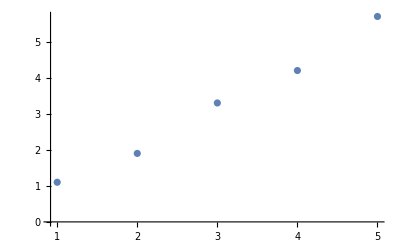

```mathematica
ListPlot[Transpose[{xdata,ydata}]]
```

```mathematica
ListPlot[xdata,ydata]
```

ListPlot::nonopt: Options expected (instead of {1.1,1.9,3.3,4.2,5.7}) beyond position 1 in ListPlot[{1,2,3,4,5},{1.1,1.9,3.3,4.2,5.7}]. An option must be a rule or a list of rules.

ListPlot[{1,2,3,4,5},{1.1,1.9,3.3,4.2,5.7}]

```mathematica
?ListPlot
```

```mathematica
n=Length[xdata]
```

5

```mathematica
A = Table[{1,xdata[[i]]},{i,1,n}] 
A //MatrixForm
```

{{1,1},{1,2},{1,3},{1,4},{1,5}}

(1 | 1
1 | 2
1 | 3
1 | 4
1 | 5)

```mathematica
grad[β_]:=2 Transpose[A].(A.β-ydata)
```

```mathematica
grad[{10,13}]
```

{457.6,1609.8}

```mathematica
η=0.001
```

0.001

```mathematica
β0 ={100,100}
β1 = β0 - η grad[β0]
β2 = β1 - η grad[β1]
```

{100,100}

{96.0324,86.1202}

{92.5209,73.8862}

```mathematica
?For
```

```mathematica
Norm[grad[β0]]
```

14435.7

```mathematica
For[β ={100,100},
Norm[grad[β]]> 0.1,,
β = β - η grad[β]
]
```

```mathematica
β
```

{-0.153002,1.13421}

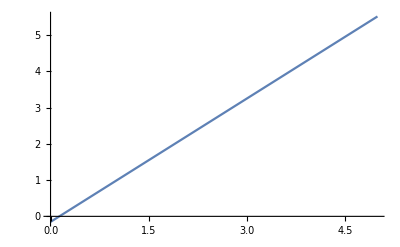

```mathematica
Plot[β[[1]] + β[[2]]x,{x,0,5}]
```

```mathematica
A=F
```